Metody numeryczne, Informatyka NS sem. III, 2023/2024

# Projekt 4 – interpolacja Lagrange’a

Napisz program, który dla argumentów wejściowych:

f – ,,nieznana” interpolowana funkcja,

a – początek przedziału,

b – koniec przedziału,

n – liczba punktów interpolacji,

realizował będzie  zagadnienie interpolacji Lagrange’a. Program dla zadanych danych wejściowych utworzy tablicę węzłów interpolacji (pierwszym węzłem jest a, ostatnim jest b, wszystkie n węzły są równoodległe) i wartości funkcji f w tych węzłach. Następnie program wygeneruje i wpisze odpowiedni wieloamin interpolacyjny Lagrange’a oraz wyświetli dwa rysunki. Na pierwszym znajdował się będzie wykres funkcji f w przedziale [a,b], wykres utworzonego wielomianu interpolacyjnego i punkty węzłowe. Na drugim  rysunku znajdował się będzie wykres błędów bezwzględnych interpolacji (moduł różnicy funkcji i jej wielomianu interpolacyjnego).
Oczywiście w rzeczywistości nie znamy funkcji f, jednak dla początkowych testów takie podejście pokazuje poprawność (lub nie) napisanego programu.

## Przykłady

### Przykład 1a.

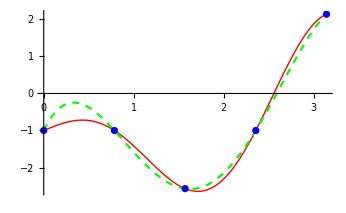
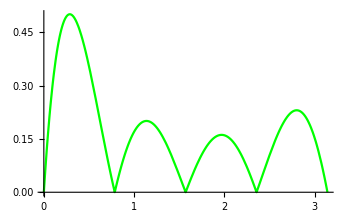
f[x_]:=x Cos[2x]-1;
interpolacjaL[f,0,Pi,5]
Wielomian:-1.+5. x-9.7615 x^2+4.86342 x^3-0.688033 x^4
-Graphics-
-Graphics-

### Przykład 1b.

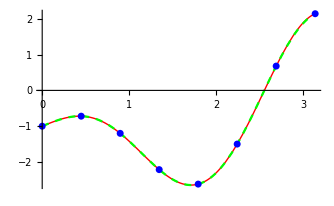
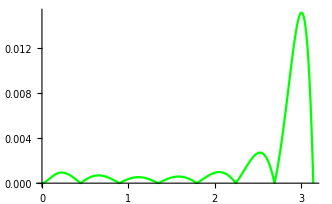
f[x_]:=x Cos[2x]-1;
interpolacjaL[f,0,Pi,8]
Wielomian:-1.+1. x-0.0867206 x^2-1.51135 x^3-1.04766 x^4+1.78008 x^5-0.616251 x^6+0.0653863 x^7
-Graphics-
-Graphics-

### Przykład 2a.

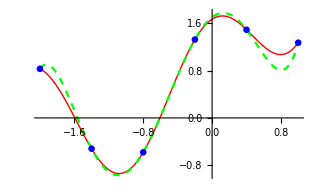
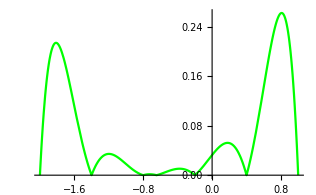
f[x_]:=E^(x)-E^ArcTan[x-2]+ Cos[3x];
interpolacjaL[f,-2,1,6]
Wielomian:1.70209+1.1087 x-4.17125 x^2-1.02206 x^3+2.64187 x^4+1.01301 x^5
-Graphics-
-Graphics-

### Przykład 2b.

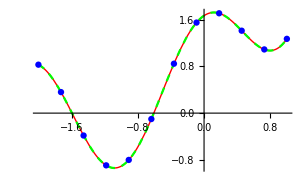
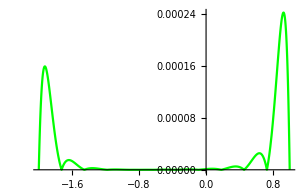
f[x_]:=E^(x)-E^ArcTan[x-2]+ Cos[3x];
interpolacjaL[f,-2,1,12]
Wielomian:1.6695+0.933889 x-4.03301 x^2+0.151588 x^3+3.41015 x^4+0.00381112 x^5-1.01507 x^6+0.001276 x^7+0.168843 x^8+0.00330843 x^9-0.0186792 x^10-0.00325108 x^11
-Graphics-
-Graphics-

### Przykład 3a.

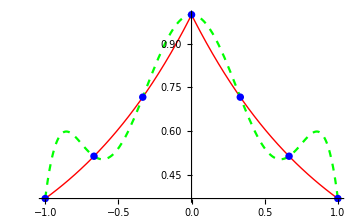
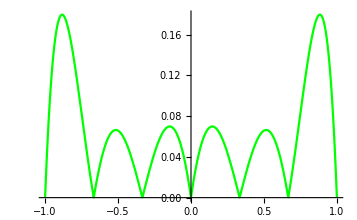
f[x_]:=Exp[-Abs[x]]; (* efekt Rungego *)
interpolacjaL[f,-1,1,7]
Wielomian:1.+8.88178×10^-16 x-3.23315 x^2-2.22045×10^-15 x^3+6.57946 x^4-1.02141×10^-14 x^5-3.97842 x^6
-Graphics-
-Graphics-

### Przykład 3b.

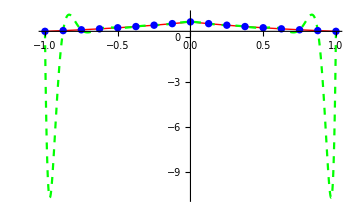
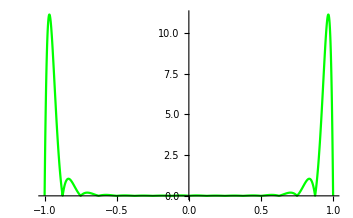
f[x_]:=Exp[-Abs[x]]; (* efekt Rungego *)
interpolacjaL[f,-1,1,17]
Wielomian:1.-1.77636×10^-15 x-10.1171 x^2-3.83693×10^-13 x^3+194.641 x^4-8.6402×10^-12 x^5-1976.1 x^6+4.84761×10^-10 x^7+10426.6 x^8+4.02724×10^-9 x^9-29876.1 x^10+8.40737×10^-9 x^11+46559.9 x^12+3.07409×10^-9 x^13-36843.7 x^14-6.36646×10^-12 x^15+11524.2 x^16
-Graphics-
-Graphics-